```mathematica
fpc = -30;
sigma2 = -19.1;
K1=1+0.92(sigma2/fpc)-0.76(sigma2/fpc)^2
```

1.27767

```mathematica
Animate[Plot[1-0.92(sigma2/fpc)-0.76(sigma2/fpc)^2,{sigma2,0,-30}],{sigma2,20},AnimationRunning->False]
```

```mathematica
epsp1=-0.0035
```

-0.0035

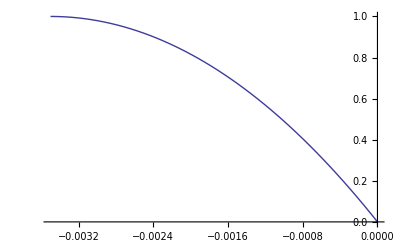

```mathematica
Plot[2(eps1/epsp1)-(eps1/epsp1)^2,{eps1,0,-0.0035}]
```

-0.0025

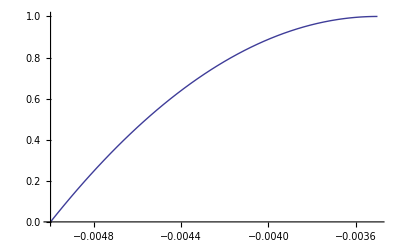

```mathematica
epsc0=-0.0025
Plot[1-(eps1-epsp1)^2/(2epsc0-epsp1)^2,{eps1,-0.0035,-0.005}]
```

```mathematica
SSPquad Bmap Matrix
Mmem=({{-0.0005, 0, -0.0005, 0, -0.0005, -0.0005, 0.0005, 0}, {-0.0005, 0, -0.0005, 0.0005, 0.0005, 0, 0.0005, 0}, {0.0005, 0.0005, -0.0005, 0, 0.0005, 0, 0.0005, -0.0005}})
u=({{0, 0, -4.6723482119  10^-7, 0, 1.496 10^-5, -0.0046277, 1.54275 10^-5, -4.6227 10^-3}})
```

Bmap Matrix SSPquad

{{-0.0005,0,-0.0005,0,-0.0005,-0.0005,0.0005,0},{-0.0005,0,-0.0005,0.0005,0.0005,0,0.0005,0},{0.0005,0.0005,-0.0005,0,0.0005,0,0.0005,-0.0005}}

{{0,0,-4.67235×10^-7,0,0.00001496,-0.0046277,0.0000154275,-0.0046227}}

```mathematica
Dot[Mmem,Transpose[u]]
```

{{2.31432×10^-6},{1.54274×10^-8},{2.32678×10^-6}}